# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"Puerto Rico","Ohio","Washington","Vermont"};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01","2022-01-15","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-16

```mathematica
states=Union[seqData[[All,2]]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Puerto Rico,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Virginia,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Alabama→{{2022-01-02,42},{2022-01-03,72},{2022-01-04,48},{2022-01-05,5},{2022-01-06,9},{2022-01-07,30},{2022-01-08,4},{2022-01-09,1},{2022-01-10,5},{2022-01-11,28},{2022-01-12,0},{2022-01-13,5},{2022-01-14,0},{2022-01-15,0},{2022-01-16,3}},Arizona→{{2022-01-02,337},{2022-01-03,412},{2022-01-04,466},{2022-01-05,408},{2022-01-06,550},{2022-01-07,339},{2022-01-08,226},{2022-01-09,362},{2022-01-10,392},{2022-01-11,391},{2022-01-12,411},{2022-01-13,176},{2022-01-14,118},{2022-01-15,15},{2022-01-16,276}},Arkansas→{{2022-01-02,9},{2022-01-03,150},{2022-01-04,147},{2022-01-05,214},{2022-01-06,83},{2022-01-07,48},{2022-01-08,3},{2022-01-09,3},{2022-01-10,127},{2022-01-11,95},{2022-01-12,37},{2022-01-13,0},{2022-01-14,0},{2022-01-15,0},{2022-01-16,0}},California→{{2022-01-02,1236},{2022-01-03,2375},{2022-01-04,2165},{2022-01-05,407},{2022-01-06,281},{2022-01-07,382},{2022-01-08,76},{2022-01-09,103},{2022-01-10,228},{2022-01-11,120},{2022-01-12,106},{2022-01-13,65},{2022-01-14,15},{2022-01-15,445},{2022-01-16,19}},Colorado→{{2022-01-02,189},{2022-01-03,870},{2022-01-04,605},{2022-01-05,267},{2022-01-06,291},{2022-01-07,874},{2022-01-08,685},{2022-01-09,147},{2022-01-10,223},{2022-01-11,107},{2022-01-12,156},{2022-01-13,4},{2022-01-14,0},{2022-01-15,0},{2022-01-16,0}},Connecticut→{{2022-01-02,192},{2022-01-03,413},{2022-01-04,273},{2022-01-05,215},{2022-01-06,181},{2022-01-07,152},{2022-01-08,68},{2022-01-09,77},{2022-01-10,38},{2022-01-11,11},{2022-01-12,4},{2022-01-13,0},{2022-01-14,0},{2022-01-15,0},{2022-01-16,1}},Delaware→{{2022-01-02,26},{2022-01-03,94},{2022-01-04,257},{2022-01-05,147},{2022-01-06,192},{2022-01-07,72},{2022-01-08,4},{2022-01-09,4},{2022-01-10,57},{2022-01-11,28},{2022-01-12,12},{2022-01-13,1},{2022-01-14,0},{2022-01-15,0},{2022-01-16,0}},Florida→{{2022-01-02,236},{2022-01-03,274},{2022-01-04,225},{2022-01-05,216},{2022-01-06,135},{2022-01-07,89},{2022-01-08,109},{2022-01-09,104},{2022-01-10,115},{2022-01-11,116},{2022-01-12,107},{2022-01-13,36},{2022-01-14,1},{2022-01-15,0},{2022-01-16,1}},Georgia→{{2022-01-02,122},{2022-01-03,272},{2022-01-04,293},{2022-01-05,152},{2022-01-06,11},{2022-01-07,11},{2022-01-08,31},{2022-01-09,26},{2022-01-10,46},{2022-01-11,60},{2022-01-12,32},{2022-01-13,20},{2022-01-14,0},{2022-01-15,1},{2022-01-16,0}},Illinois→{{2022-01-02,71},{2022-01-03,203},{2022-01-04,207},{2022-01-05,67},{2022-01-06,41},{2022-01-07,47},{2022-01-08,37},{2022-01-09,33},{2022-01-10,30},{2022-01-11,22},{2022-01-12,18},{2022-01-13,17},{2022-01-14,15},{2022-01-15,7},{2022-01-16,16}},Indiana→{{2022-01-02,41},{2022-01-03,66},{2022-01-04,91},{2022-01-05,62},{2022-01-06,55},{2022-01-07,35},{2022-01-08,24},{2022-01-09,38},{2022-01-10,63},{2022-01-11,65},{2022-01-12,64},{2022-01-13,43},{2022-01-14,8},{2022-01-15,1},{2022-01-16,0}},Louisiana→{{2022-01-02,195},{2022-01-03,147},{2022-01-04,53},{2022-01-05,181},{2022-01-06,151},{2022-01-07,64},{2022-01-08,18},{2022-01-09,18},{2022-01-10,28},{2022-01-11,14},{2022-01-12,29},{2022-01-13,27},{2022-01-14,6},{2022-01-15,23},{2022-01-16,1}},Maryland→{{2022-01-02,146},{2022-01-03,243},{2022-01-04,327},{2022-01-05,192},{2022-01-06,150},{2022-01-07,76},{2022-01-08,75},{2022-01-09,41},{2022-01-10,99},{2022-01-11,73},{2022-01-12,31},{2022-01-13,28},{2022-01-14,6},{2022-01-15,5},{2022-01-16,5}},Massachusetts→{{2022-01-02,1047},{2022-01-03,1748},{2022-01-04,1590},{2022-01-05,1023},{2022-01-06,1017},{2022-01-07,577},{2022-01-08,419},{2022-01-09,1334},{2022-01-10,1108},{2022-01-11,641},{2022-01-12,254},{2022-01-13,585},{2022-01-14,130},{2022-01-15,15},{2022-01-16,1}},Michigan→{{2022-01-02,52},{2022-01-03,267},{2022-01-04,82},{2022-01-05,61},{2022-01-06,49},{2022-01-07,23},{2022-01-08,27},{2022-01-09,31},{2022-01-10,70},{2022-01-11,26},{2022-01-12,47},{2022-01-13,47},{2022-01-14,15},{2022-01-15,0},{2022-01-16,0}},Minnesota→{{2022-01-02,159},{2022-01-03,130},{2022-01-04,122},{2022-01-05,71},{2022-01-06,93},{2022-01-07,166},{2022-01-08,45},{2022-01-09,54},{2022-01-10,110},{2022-01-11,96},{2022-01-12,49},{2022-01-13,25},{2022-01-14,24},{2022-01-15,15},{2022-01-16,15}},Nebraska→{{2022-01-02,38},{2022-01-03,52},{2022-01-04,59},{2022-01-05,47},{2022-01-06,55},{2022-01-07,56},{2022-01-08,43},{2022-01-09,22},{2022-01-10,76},{2022-01-11,72},{2022-01-12,95},{2022-01-13,97},{2022-01-14,34},{2022-01-15,14},{2022-01-16,31}},Nevada→{{2022-01-02,11},{2022-01-03,58},{2022-01-04,94},{2022-01-05,119},{2022-01-06,22},{2022-01-07,30},{2022-01-08,15},{2022-01-09,14},{2022-01-10,51},{2022-01-11,37},{2022-01-12,6},{2022-01-13,28},{2022-01-14,2},{2022-01-15,0},{2022-01-16,0}},New Jersey→{{2022-01-02,56},{2022-01-03,370},{2022-01-04,931},{2022-01-05,729},{2022-01-06,119},{2022-01-07,65},{2022-01-08,25},{2022-01-09,25},{2022-01-10,83},{2022-01-11,140},{2022-01-12,118},{2022-01-13,4},{2022-01-14,8},{2022-01-15,2},{2022-01-16,1}},New Mexico→{{2022-01-02,52},{2022-01-03,110},{2022-01-04,81},{2022-01-05,66},{2022-01-06,75},{2022-01-07,60},{2022-01-08,9},{2022-01-09,9},{2022-01-10,34},{2022-01-11,6},{2022-01-12,11},{2022-01-13,0},{2022-01-14,1},{2022-01-15,1},{2022-01-16,1}},New York→{{2022-01-02,758},{2022-01-03,544},{2022-01-04,568},{2022-01-05,701},{2022-01-06,397},{2022-01-07,246},{2022-01-08,442},{2022-01-09,387},{2022-01-10,505},{2022-01-11,451},{2022-01-12,171},{2022-01-13,128},{2022-01-14,1},{2022-01-15,0},{2022-01-16,0}},North Carolina→{{2022-01-02,95},{2022-01-03,273},{2022-01-04,429},{2022-01-05,190},{2022-01-06,86},{2022-01-07,149},{2022-01-08,113},{2022-01-09,89},{2022-01-10,117},{2022-01-11,73},{2022-01-12,69},{2022-01-13,52},{2022-01-14,48},{2022-01-15,29},{2022-01-16,20}},North Dakota→{{2022-01-02,42},{2022-01-03,70},{2022-01-04,40},{2022-01-05,102},{2022-01-06,19},{2022-01-07,63},{2022-01-08,24},{2022-01-09,88},{2022-01-10,29},{2022-01-11,124},{2022-01-12,36},{2022-01-13,32},{2022-01-14,51},{2022-01-15,123},{2022-01-16,30}},Oregon→{{2022-01-02,42},{2022-01-03,190},{2022-01-04,352},{2022-01-05,266},{2022-01-06,180},{2022-01-07,150},{2022-01-08,76},{2022-01-09,17},{2022-01-10,44},{2022-01-11,19},{2022-01-12,49},{2022-01-13,9},{2022-01-14,1},{2022-01-15,0},{2022-01-16,0}},Pennsylvania→{{2022-01-02,66},{2022-01-03,91},{2022-01-04,343},{2022-01-05,47},{2022-01-06,56},{2022-01-07,44},{2022-01-08,16},{2022-01-09,20},{2022-01-10,33},{2022-01-11,49},{2022-01-12,59},{2022-01-13,14},{2022-01-14,0},{2022-01-15,30},{2022-01-16,2}},South Carolina→{{2022-01-02,30},{2022-01-03,99},{2022-01-04,145},{2022-01-05,96},{2022-01-06,3},{2022-01-07,4},{2022-01-08,11},{2022-01-09,1},{2022-01-10,7},{2022-01-11,4},{2022-01-12,3},{2022-01-13,1},{2022-01-14,0},{2022-01-15,0},{2022-01-16,0}},Tennessee→{{2022-01-02,85},{2022-01-03,80},{2022-01-04,25},{2022-01-05,22},{2022-01-06,28},{2022-01-07,32},{2022-01-08,65},{2022-01-09,22},{2022-01-10,49},{2022-01-11,16},{2022-01-12,12},{2022-01-13,2},{2022-01-14,4},{2022-01-15,0},{2022-01-16,1}},Texas→{{2022-01-02,79},{2022-01-03,408},{2022-01-04,365},{2022-01-05,211},{2022-01-06,66},{2022-01-07,90},{2022-01-08,42},{2022-01-09,27},{2022-01-10,31},{2022-01-11,38},{2022-01-12,32},{2022-01-13,13},{2022-01-14,0},{2022-01-15,0},{2022-01-16,3}},Utah→{{2022-01-02,41},{2022-01-03,659},{2022-01-04,712},{2022-01-05,379},{2022-01-06,232},{2022-01-07,182},{2022-01-08,137},{2022-01-09,12},{2022-01-10,379},{2022-01-11,314},{2022-01-12,248},{2022-01-13,122},{2022-01-14,157},{2022-01-15,185},{2022-01-16,12}},Virginia→{{2022-01-02,34},{2022-01-03,63},{2022-01-04,113},{2022-01-05,25},{2022-01-06,17},{2022-01-07,9},{2022-01-08,1},{2022-01-09,2},{2022-01-10,5},{2022-01-11,1},{2022-01-12,7},{2022-01-13,0},{2022-01-14,0},{2022-01-15,0},{2022-01-16,0}},Wisconsin→{{2022-01-02,60},{2022-01-03,165},{2022-01-04,162},{2022-01-05,38},{2022-01-06,106},{2022-01-07,149},{2022-01-08,16},{2022-01-09,18},{2022-01-10,77},{2022-01-11,30},{2022-01-12,57},{2022-01-13,12},{2022-01-14,6},{2022-01-15,0},{2022-01-16,1}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

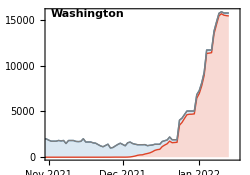

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

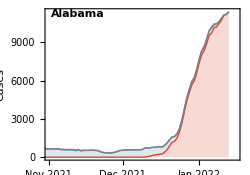
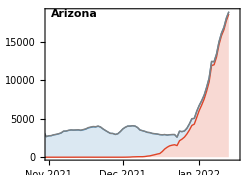
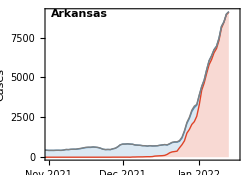
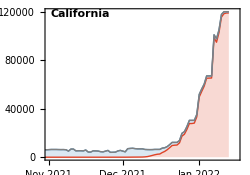
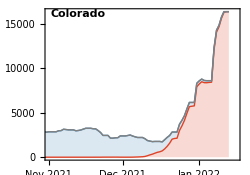
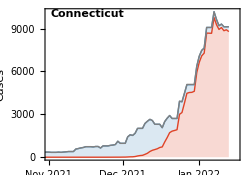
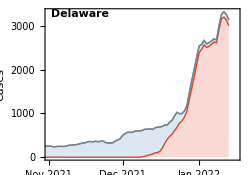
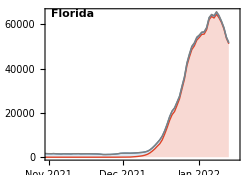
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png